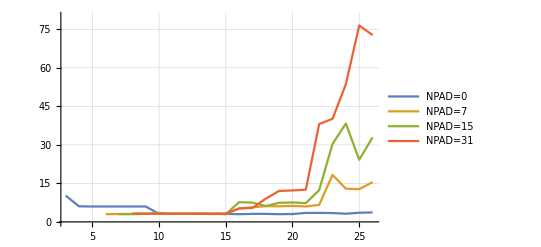

```mathematica
NPAD0Linear={{3,10.25},{4,6.0625},{5,6},{6,6},{7,6},{8,6},{9,6},{10,3.125},{11,3.125},{12,3.125},{13,3.1875},{14,3.0625},{15,3.125},{16,3},{17,3.125},{18,3.125},{19,3},{20,3.0625},{21,3.5},{22,3.5},{23,3.4375},{24,3.1875},{25,3.5625},{26,3.6875},};
NPAD7Linear={{6,3},{7,3.0625},{8,3.125},{9,3.125},{10,3.125},{11,3.125},{12,3.1875},{13,3.1875},{14,3.25},{15,3.0625},{16,5.3125},{17,5.6875},{18,6.125},{19,6.0625},{20,6.25},{21,6},{22,6.625},{23,18.3125},{24,12.9375},{25,12.75},{26,15.5},};
NPAD15Linear={{7,3},{8,3},{9,3.1875},{10,3.5},{11,3.1875},{12,3.125},{13,3.1875},{14,3.25},{15,3},{16,7.6875},{17,7.5},{18,6.1875},{19,7.4375},{20,7.5625},{21,7.3125},{22,12.375},{23,30.375},{24,38.3125},{25,24.1875},{26,32.9375},};
NPAD31Linear={{8,3.25},{9,3.1875},{10,3.1875},{11,3.1875},{12,3.1875},{13,3.1875},{14,3.125},{15,3.25},{16,5.1875},{17,5.4375},{18,9.0625},{19,12.0625},{20,12.25},{21,12.5625},{22,38.125},{23,40.125},{24,53.625},{25,76.5},{26,72.75},};
ListPlot[{NPAD0Linear,NPAD7Linear,NPAD15Linear,NPAD31Linear},GridLines->Automatic,Ticks->Automatic,Joined->True,PlotLegends->{"NPAD=0", "NPAD=7","NPAD=15","NPAD=31"},PlotRange->80]
```

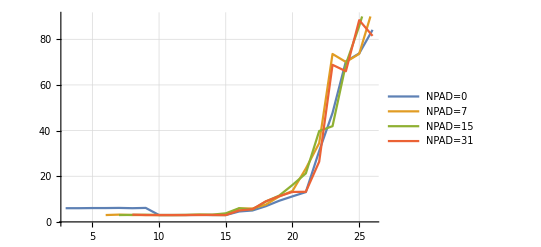

```mathematica
NPAD0Random={{3,6},{4,6},{5,6.0625},{6,6.0625},{7,6.125},{8,6},{9,6.125},{10,3},{11,3},{12,3},{13,3.0625},{14,3},{15,3},{16,4.5625},{17,5},{18,6.875},{19,9.25},{20,11.1875},{21,13.0625},{22,31.0625},{23,47.75},{24,70.3125},{25,73.8125},{26,84.125},};
NPAD7Random={{6,3},{7,3.1875},{8,3},{9,3},{10,3},{11,3},{12,3},{13,3.1875},{14,3},{15,3},{16,5.875},{17,5.875},{18,7.5625},{19,11.125},{20,13.5625},{21,23.375},{22,34.5},{23,73.5625},{24,70.0625},{25,73.625},{26,93.125},};
NPAD15Random={{7,3},{8,3.0625},{9,3.125},{10,3},{11,3},{12,3.0625},{13,3.125},{14,3.1875},{15,3.75},{16,6},{17,5.4375},{18,8.9375},{19,11.5},{20,16.1875},{21,21.25},{22,39.8125},{23,41.9375},{24,69.0625},{25,85.8125},{26,105.125},};
NPAD31Random={{8,3.1875},{9,3},{10,3},{11,3},{12,3},{13,3},{14,3.0625},{15,3},{16,5},{17,5.5625},{18,9},{19,11.25},{20,13.125},{21,13.1875},{22,26.375},{23,68.8125},{24,66},{25,88.375},{26,81.5},};
ListPlot[{NPAD0Random,NPAD7Random,NPAD15Random,NPAD31Random},GridLines->Automatic,Ticks->Automatic,Joined->True,PlotLegends->{"NPAD=0", "NPAD=7","NPAD=15","NPAD=31"},PlotRange->90]
```

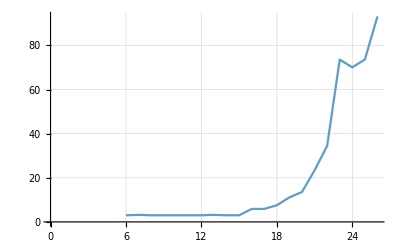

```mathematica
ListLinePlot[NPAD7Random,GridLines->Automatic]
```